```mathematica
Plot3D[Exp[-x^2] Exp[-y^2] Sin[10 x]^2 Sin[10 y]^2 Sin[x+y]^2,{x,-2,2},{y,-2,2},PlotRange->Full,PlotPoints->100]
```

-Graphics3D-

```mathematica
NIntegrate[Exp[-x^2] Exp[-y^2] Sin[10 x]^2 Sin[10 y]^2 Sin[x+y]^2,{x,-2,2},{y,-2,2}]
```

0.334642

```mathematica
NumberForm[0.33464230199216916,16]
```

0.3346423019921692

```mathematica
N@(1/(128 ⅇ^242))π (16 ⅇ^242 Erf[2]^2-4 ⅇ^240 (Erf[2+ⅈ]-ⅈ Erfi[1+2 ⅈ])^2+4 ⅇ^160 (Erf[2+ⅈ]-ⅈ Erfi[1+2 ⅈ]) (Erf[2+9 ⅈ]-ⅈ Erfi[9+2 ⅈ])-ⅇ^80 (Erf[2+9 ⅈ]-ⅈ Erfi[9+2 ⅈ])^2-16 ⅇ^142 Erf[2] (Erf[2+10 ⅈ]-ⅈ Erfi[10+2 ⅈ])+4 ⅇ^42 (Erf[2+10 ⅈ]-ⅈ Erfi[10+2 ⅈ])^2+4 ⅇ^120 (Erf[2+ⅈ]-ⅈ Erfi[1+2 ⅈ]) (Erf[2+11 ⅈ]-ⅈ Erfi[11+2 ⅈ])-2 ⅇ^40 (Erf[2+9 ⅈ]-ⅈ Erfi[9+2 ⅈ]) (Erf[2+11 ⅈ]-ⅈ Erfi[11+2 ⅈ])-(Erf[2+11 ⅈ]-ⅈ Erfi[11+2 ⅈ])^2)
```

0.334642+0. ⅈ

```mathematica
Integrate[Exp[-x^2] Sin[10 x]^2,{x,-2,2}]
```

```mathematica
N@((√π (2 ⅇ^100 Erf[2]-Erf[2+10 ⅈ]+ⅈ Erfi[10+2 ⅈ]))/(4 ⅇ^100))
```

0.881303+0. ⅈ

## Make it a little harder

```mathematica
Plot3D[Exp[-Abs[x]] Exp[-y^2] Sin[10 x]^2 Sin[10 y]^2 Sin[x+y]^2,{x,-2,2},{y,-2,2},PlotRange->Full,PlotPoints->100]
```

-Graphics3D-

## Try a harder integral from here: https://mathematica.stackexchange.com/questions/33217/mathematica-computing-a-difficult-integral?rq=1 Actually not sure that this is that hard since it looks Gaussian

```mathematica
Exp[Sum[-((cw λ-b[i])^2/(2 σ^2)),{i,1,n}]]
```

ⅇ^(∑_(i=1)^n -(cw λ-b[i])^2/(2 σ^2))

```mathematica
Integrate[Exp[Sum[-((cw λ-b[i])^2/(2 σ^2)),{i,1,n}]],{cw,0,1}]
```

$Aborted

```mathematica
Clear[b]
```

```mathematica
Integrate[Exp[(-n cw^2 λ^2+2 cw λ Sum[b[i],{i,1,n}]-Sum[b[i]^2,{i,1,n}])/(2 σ^2)],{cw,0,1}]
```

(ⅇ^(((∑_(i=1)^n b[i])^2-n ∑_(i=1)^n b[i]^2)/(2 n σ^2)) √(π/2) σ (Erf[(n λ-∑_(i=1)^n b[i])/(√2 √n σ)]+Erf[(∑_(i=1)^n b[i])/(√2 √n σ)]))/(√n λ)

```mathematica
(ⅇ^(((∑_(i=1)^n b[i])^2-n ∑_(i=1)^n b[i]^2)/(2 n σ^2)) √(π/2) σ (Erf[(n λ-∑_(i=1)^n b[i])/(√2 √n σ)]+Erf[(∑_(i=1)^n b[i])/(√2 √n σ)]))/(√n λ)
```

```mathematica
Table[b[i]=RandomVariate[NormalDistribution[]],{i,1,100,1}];
n=1;
```

```mathematica
(ⅇ^(((∑_(i=1)^n b[i])^2-n ∑_(i=1)^n b[i]^2)/(2 n σ^2)) √(π/2) σ (Erf[(n λ-∑_(i=1)^n b[i])/(√2 √n σ)]+Erf[(∑_(i=1)^n b[i])/(√2 √n σ)]))/(√n λ)
```

(1.25331 σ (-Erf[1.65854/σ]+Erf[(2.34553+λ)/(√2 σ)]))/λ

```mathematica
analyticIntegral[b_,n_,λ_,σ_]:=Block[{},(ⅇ^(((∑_(i=1)^n b[i])^2-n ∑_(i=1)^n b[i]^2)/(2 n σ^2)) √(π/2) σ (Erf[(n λ-∑_(i=1)^n b[i])/(√2 √n σ)]+Erf[(∑_(i=1)^n b[i])/(√2 √n σ)]))/(√n λ)]
```

```mathematica
analyticIntegral[b,100,1,1]
```

1.50405×10^-22

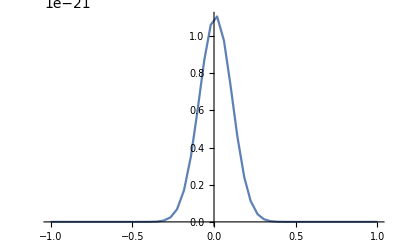

```mathematica
Plot[Exp[Sum[-((cw λ-b[i])^2/(2 σ^2)),{i,1,100,1}]]/.{λ->1,σ->1},{cw,-1,1},PlotRange->Full]
```

```mathematica
NIntegrate[Exp[Sum[-((cw λ-b[i])^2/(2 σ^2)),{i,1,100,1}]]/.{λ->1,σ->1},{cw,0,1}]
```

1.50405×10^-22